## Initialization

```mathematica
rat[i_Integer,m_Integer,b_Integer,v_Integer]:=ArrayPlot[PadLeft[IntegerDigits[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m],v]]]
countRat[i_Integer,m_Integer,b_Integer]:=Length[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m]]-1
listRat[i_Integer,m_Integer,b_Integer]:=Column[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m]]
listRat2[i_Integer,m_Integer,b_Integer]:=Column[FromDigits /@ IntegerDigits[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m],b]]
finalRat[i_Integer,m_Integer,b_Integer,v_Integer]:={rat[i,m,b,v],listRat[i,m,b],listRat2[i,m,b],countRat[i,m,b],ftrRat[i,m,b]}
ftrRat[i_Integer,m_Integer,b_Integer]:=If[FindTransientRepeat[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m],2][[2]]=!={},NestGraph[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m,VertexLabels->"Name"],"No repeating patten detected"]
```

## Program

```mathematica
Manipulate[Grid[{{"visual representation in base "<>ToString[v],"numbers after each iteration in base 10","numbers after each iteration in base "<>ToString[b],"number of iterations", "NestGraph (if there is a repeating pattern)"},finalRat[i,m,b,v]},Frame->All],{{i,10,"initial value in base 10 (click enter after input)"},ControlType-> InputField},{{m,1,"max number of iterations"},1,500,1,Appearance-> "Labeled"},{{b,10,"base to compute 196-algorithm"}, 2,10,1, ControlType-> PopupMenu},{{v,2,"base to represent iterations"}, 2,10,1, ControlType-> PopupMenu}]
```

```mathematica
rat[#,50,10,2]& /@ {879,196,7059,1997,9999,80049,80059,40069,80069,13097,14096,89099,13197,80269,80279,60289,80289,15297,59299,70379,90379,30389,30399,40429,80439,20459,60489,80489,10553,70559,10563,50569,10577,50579,90579,10583,10585,15597,18598,10638,60659,10663,10668,80669,60689,10697,13694,14698,10715,10728,10735,10746,10748,10783,10785,10787,10788,12797,18798,10877,10883,12898,89899,30929,70949,30959,10963,10965,10969,10977,30979,10983,10985,99999,140096,150096,990099,150195,790199,130295,150297,490299,990299,150397,490399,690399,890399,130494,130495,140496,490499,790499,890499,990499,700509,150595,150597,700699,150695,190699,290699,790699,890699,990699,300709,890799,700899,590899,990899,700909,300929,700949,190997,101917,101948,101968,101976,102918,102988,103905,103908,103927,103937,103986,104905,104907,104927,104947,104948,104956,104958,104968,105917,105925,105968,105998,125997,106918,106938,106976,106982,106988,107917,107938,107967,107968,107985,117994,108907,108936,108937,108947,108953,108957,108976,108978,108985,118994,109908,109918,109958,109963,109967,109980,119994,129995,139994,149995,149998,199999,399999,499999,999999,7000069,6000089,8000089,1500097,8900099,8000199,9000199,1400196,1800196,1900196,8000299,1300297,1500295,6900299,1000379,9000399,1700396,6900399,8900399,1000469,6000499,7000499,8000499,1300495,1500497,1600497}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ftrRat[i_Integer,m_Integer,b_Integer]:=If[FindTransientRepeat[NestList[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m],2][[2]]=!={},NestGraph[(FromDigits[Sort[IntegerDigits[IntegerReverse[#,b]+#]]])&,i,m,VertexLabels->"Name"],"No repeating patten detected"]
```

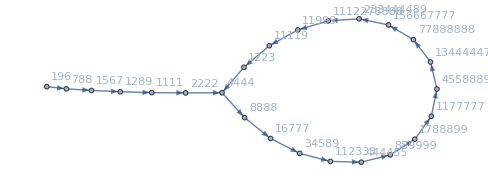

```mathematica
ftrRat[196, 50,10]
```